### Start choosing the example:

```mathematica
t=12;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 10.9691 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{13.1456,Null}

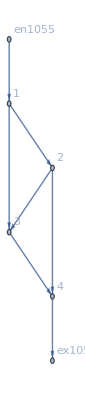

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→95.,u1096→95.,u1097→55.,u1098→55.,u1099→55.,u1100→15.,u1101→95.,u1102→55.,u1103→55.,u1104→55.,u1105→15.,u1106→15.,u1107→15.,u1108→95.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.16139×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.16139×10^-16

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→19.6805,u1096→19.6805,u1097→17.3402,u1098→17.3402,u1099→17.3402,u1100→15.,u1101→19.6805,u1102→17.3402,u1103→17.3402,u1104→17.3402,u1105→15.,u1106→15.,u1107→15.,u1108→19.6805|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.54409×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.54409×10^-17

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→20.5515,u1096→20.5515,u1097→17.7758,u1098→17.7758,u1099→17.7758,u1100→15.,u1101→20.5515,u1102→17.7758,u1103→17.7758,u1104→17.7758,u1105→15.,u1106→15.,u1107→15.,u1108→20.5515|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.42094×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.42094×10^-17

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→23.1887,u1096→23.1887,u1097→19.0944,u1098→19.0944,u1099→19.0944,u1100→15.,u1101→23.1887,u1102→19.0944,u1103→19.0944,u1104→19.0944,u1105→15.,u1106→15.,u1107→15.,u1108→23.1887|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.35438×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.35438×10^-16

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→65.0434,u1096→65.0434,u1097→40.0217,u1098→40.0217,u1099→40.0217,u1100→15.,u1101→65.0434,u1102→40.0217,u1103→40.0217,u1104→40.0217,u1105→15.,u1106→15.,u1107→15.,u1108→65.0434|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[8.52651×10^-14,ComplexInfinity]

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→95.,u1096→95.,u1097→55.,u1098→55.,u1099→55.,u1100→15.,u1101→95.,u1102→55.,u1103→55.,u1104→55.,u1105→15.,u1106→15.,u1107→15.,u1108→95.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→286.7,u1096→286.7,u1097→150.85,u1098→150.85,u1099→150.85,u1100→15.,u1101→286.7,u1102→150.85,u1103→150.85,u1104→150.85,u1105→15.,u1106→15.,u1107→15.,u1108→286.7|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→7208.19,u1096→7208.19,u1097→3611.59,u1098→3611.59,u1099→3611.59,u1100→15.,u1101→7208.19,u1102→3611.59,u1103→3611.59,u1104→3611.59,u1105→15.,u1106→15.,u1107→15.,u1108→7208.19|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→2.99468×10^14,u1096→2.99468×10^14,u1097→1.49734×10^14,u1098→1.49734×10^14,u1099→1.49734×10^14,u1100→15.,u1101→2.99468×10^14,u1102→1.49734×10^14,u1103→1.49734×10^14,u1104→1.49734×10^14,u1105→15.,u1106→15.,u1107→15.,u1108→2.99468×10^14|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.707107

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.707107

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

<|j1057→40.,j1058→40.,j1059→0,j1060→40.,j1061→40.,j1062→80.,j1063→80.,j1064→0,j1065→0.,j1066→0,j1067→0.,j1068→0.,j1069→0.,j1070→0.,jt1071→0.,jt1072→0.,jt1073→0.,jt1074→0.,jt1075→40.,jt1076→40.,jt1077→0,jt1078→40.,jt1079→0.,jt1080→0.,jt1081→0.,jt1082→0.,jt1083→0,jt1084→40.,jt1085→0.,jt1086→0.,jt1087→0.,jt1088→0.,jt1089→0.,jt1090→40.,jt1091→0.,jt1092→40.,jt1093→0.,jt1094→0.,u1095→95.,u1096→95.,u1097→55.,u1098→55.,u1099→55.,u1100→15.,u1101→95.,u1102→55.,u1103→55.,u1104→55.,u1105→15.,u1106→15.,u1107→15.,u1108→95.|>